```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

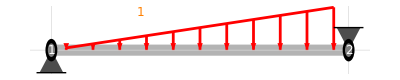

```mathematica
example={$$nodes->{{-L, 0}, {0, 0}},
$$edges->{{1, 2}},$$absname->s,
$$constraints->{{{"hinge", 1}}, {{"hinge", 1}}},
$$bodyloads->{{1, {0, -(q*s)/L, 0}}},
$$nodalloads->{{1, {0, 0, 0}}},
$$predeformations->{{1, {0, 0, 0}}},
$$cdisplacements->{{1, {0, 0, 0}}},
$$EIoverEAL2->0};
(*All constraints are initialized to hinge constraints; use "BFConstraintsPalette[BFConstraintTypes];" to input different constraints.*)
BFShowInput[example]
```

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
(*BFClassify[example]; sol = {{Ns, Qs, Ms}, details} = BFForcesSolve[example];*)
(*A=Transpose[First[BFStaticProblem[example]]];MatrixForm[A]
BFShowRigidMotions[example]*)
BFEquations[example,"Nodal"]; sol = {{us, vs}, {Ns, Qs, Ms}, details} = BFDisplacementsSolve[example];
gsol=BFShowOutput[example, sol]
```

Natural constraints in node 1: M_1[0]==0

Natural constraints in node 2: -M_1[1]==0

Kinematical constraints in node 1: u_1[0]==0
v_1[0]==0

Kinematical constraints in node 2: u_1[1]==0
v_1[1]==0

Infinity::indet: Indeterminate expression 0 ∞ encountered.

1234

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Ascissa adimensionale

s

Vincoli statici nei nodi

{{("M")_("1")[0]==0},{-("M")_("1")[1]==0}}

Vincoli cinematici nei nodi

{{("u")_("1")[0]==0,("v")_("1")[0]==0},{("u")_("1")[1]==0,("v")_("1")[1]==0}}

Lista rigidezze flessionali

{EI}

Lista rigidezze assiali

{∞}

Lunghezze delle travi

{L}

Equazioni di campo (o della linea elastica)

{("u")_("1")''[s]==0,(("v")_("1"))^(4)[s]==-(L^3 q s)/EI}

Condizioni al contorno in spostamenti

{("u")_("1")[0]==0,("v")_("1")[0]==0,("u")_("1")[1]==0,("v")_("1")[1]==0,EI ("v")_("1")''[0]==0,EI ("v")_("1")''[1]==0}

Soluzione in spostamenti

{{0},{-(L^3 q (7 s-10 s^3+3 s^5))/(360 EI)}}

Soluzione in sollecitazioni

{{Indeterminate},{1/6 q (-1+3 s^2)},{-1/6 L q s (-1+s^2)}}

-Graphics-

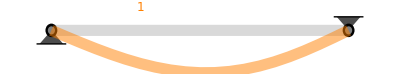

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
-D[(L^3 q (7 s-10 s^3+3 s^5))/(360 EI),s]/.s->1
```

(L^3 q)/(45 EI)